```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/4.1/4.1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/4.1/~$4.1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/4.1/4.1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset 1

```mathematica
dataset1 =raw⟦3⟧⟦2;;⟧
```

{{0.,8.},{3.4,42.},{17.,188.},{30.6,348.},{44.2,522.},{57.8,711.},{59.16,733.},{60.52,754.},{61.88,772.},{63.24,793.},{64.6,816.},{65.96,835.},{67.32,851.},{68.68,875.},{70.04,895.},{71.4,908.},{71.4,911.},{72.76,928.},{74.12,931.},{75.48,941.},{76.84,943.},{78.2,946.},{79.56,951.},{80.92,947.},{82.28,946.},{83.64,947.},{85.,935.},{87.72,935.},{90.44,932.},{93.16,929.},{95.88,924.},{98.6,918.},{99.28,913.}}

```mathematica
dataset1line2=dataset1⟦-15;;⟧⟦;;7⟧
```

{{74.12,931.},{75.48,941.},{76.84,943.},{78.2,946.},{79.56,951.},{80.92,947.},{82.28,946.}}

```mathematica
dataset1line = dataset1⟦8;;15⟧
```

{{60.52,754.},{61.88,772.},{63.24,793.},{64.6,816.},{65.96,835.},{67.32,851.},{68.68,875.},{70.04,895.}}

```mathematica
line1 = LinearModelFit[dataset1line, {1,x},x]
```

FittedModel[-144.696+14.8372 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -144.696 | 13.3798 | -10.8145 | 0.0000369986
x | 14.8372 | 0.204727 | 72.473 | 4.64457×10^-10

```mathematica
line2 = LinearModelFit[dataset1line2, {1},x]
```

FittedModel[943.571]

```mathematica
line2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 943.571 | 2.40888 | 391.705 | 1.86855×10^-14

## Plot1

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

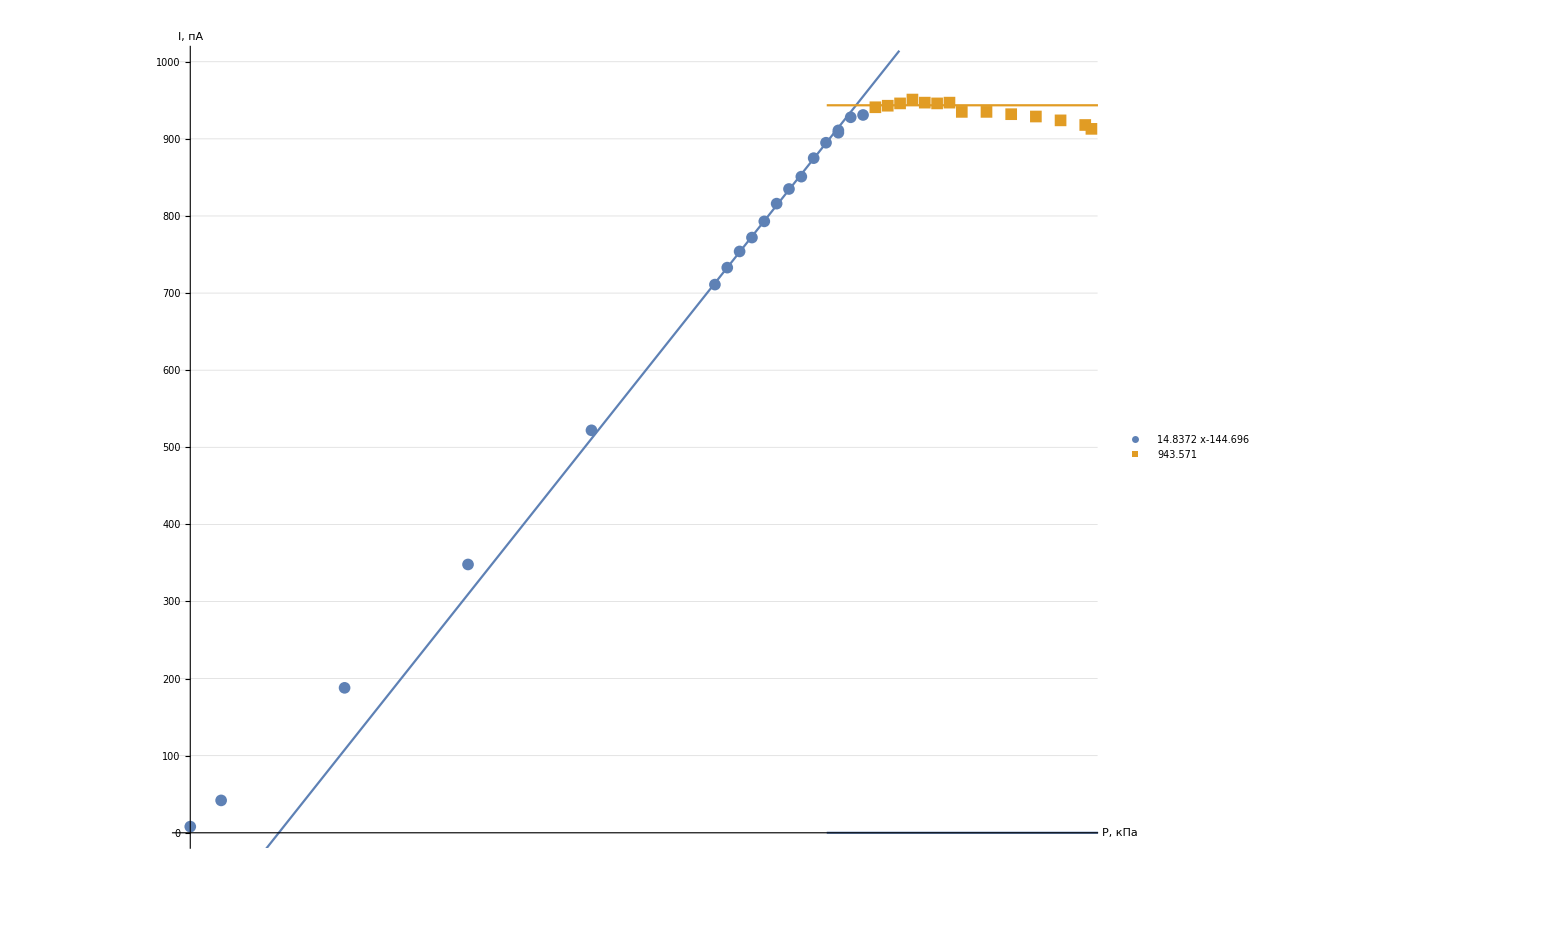

```mathematica
Show[
ListPlot[
{dataset1⟦;;19⟧,dataset1⟦20;;⟧},
PlotRange-> {{0,98},{0,1000}},
Ticks-> {Range[-1000,1000, 5],Range[-1000,1000, 50]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["P, кПа", Large], Style["I, пА", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 2.5],Range[-1000,1000, 25]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
{Normal@line1,Normal@line2},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.75]}
]
],
Plot[{line1[x]},{x,0,78.12}],
Plot[{0,line2[x]},{x,70.12,100}]
]
```

## Dataset 2

```mathematica
dataset2 =raw⟦4⟧⟦2;;⟧
```

{{0.,364.5},{3.4,345.1},{6.12,336.8},{8.84,325.2},{11.56,295.6},{14.28,284.8},{17.,238.1},{19.72,215.4},{22.44,181.2},{25.16,138.4},{27.88,99.7},{30.6,63.},{31.96,49.2},{33.32,35.2},{34.68,22.2},{36.04,8.},{37.4,3.6},{38.76,1.11},{44.2,0.12},{57.8,0.16}}

```mathematica
dataset2line = dataset2⟦6;;12⟧
```

{{14.28,284.8},{17.,238.1},{19.72,215.4},{22.44,181.2},{25.16,138.4},{27.88,99.7},{30.6,63.}}

```mathematica
line3=LinearModelFit[dataset2line,{1,x},x]
```

FittedModel[474.671-13.3824 x]

```mathematica
line3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 474.671 | 9.08229 | 52.2634 | 4.84857×10^-8
x | -13.3824 | 0.393343 | -34.0221 | 4.12562×10^-7

## Plot2

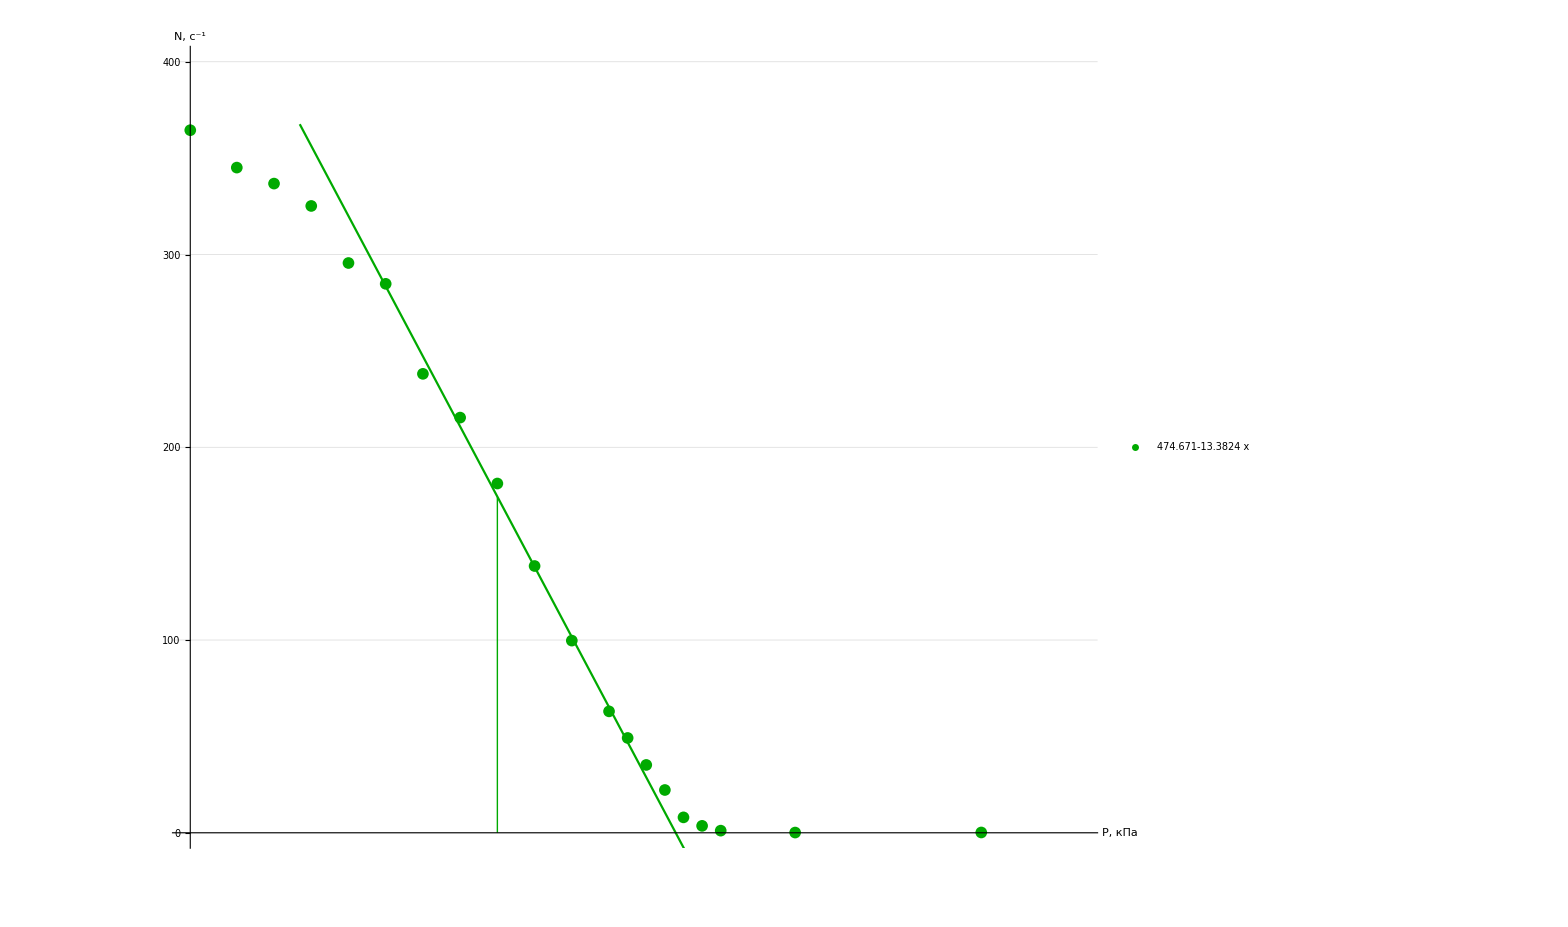

```mathematica
Show[
ListPlot[
{dataset2},
PlotRange-> {{0,65},{0,400}},
Ticks-> {Range[-1000,1000, 5],Range[-1000,1000, 50]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["P, кПа", Large], Style["N, (:0441)^-1", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
PlotStyle->Darker@Green,
GridLines-> {Range[-1000,1000, 2],Range[-1000,1000, 20]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
{Normal@line3},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.6],Scaled[0.75]}
],
Epilog->{Darker@Green,Thickness->0.0012,Line[{{22.44,0},{22.44,174}}]}
],
Plot[{line3[x]},{x,8,78.12},PlotStyle->Darker@Green](*,
Plot[{0,line2[x]},{x,70.12,100}]*)
]
```